```mathematica
SetDirectory[NotebookDirectory[]];
```

# T_scaling

## data

```mathematica
fpi=Flatten[Import["./LPA_Tscaling_mub0/buffer/mSigma.dat"]];
T0=Flatten[Import["./LPA_Tscaling_mub0/buffer/TMeV.dat"]];
t=-(T0-T0[[1]])/T0[[1]];
datamub0=Transpose[{Log[-t[[2;;Length[t]]]],Log[1/fpi[[2;;Length[t]]]]}];
b1mub0=Transpose[{Log[-t[[2;;Length[t]-2]]],-Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];

fpi=Flatten[Import["./LPA_Tscaling_mub700/buffer/mSigma.dat"]];
T700=Flatten[Import["./LPA_Tscaling_mub700/buffer/TMeV.dat"]];
t=-(T700-T700[[1]])/T700[[1]];
datamub700=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub700=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub700[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T700]-2}]]}];

fpi=Flatten[Import["./LPA_Tscaling_mub705/buffer/mSigma.dat"]];
T705=Flatten[Import["./LPA_Tscaling_mub705/buffer/TMeV.dat"]];
t=-(T705-T705[[1]])/T705[[1]];
datamub705=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub705=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub705[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T705]-2}]]}];

fpi=Flatten[Import["./LPA_Tscaling_mub706/buffer/mSigma.dat"]];
T706=Flatten[Import["./LPA_Tscaling_mub706/buffer/TMeV.dat"]];
t=-(T706-T706[[1]])/T706[[1]];
datamub706=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub706=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub706[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T706]-2}]]}];

fpi=Flatten[Import["./LPA_Tscaling_mub706p3/buffer/mSigma.dat"]];
T=Flatten[Import["./LPA_Tscaling_mub706p3/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub706p3=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];

fpi=Flatten[Import["./LPA_Tscaling_mub706p4/buffer/mSigma.dat"]];
T=Flatten[Import["./LPA_Tscaling_mub706p4/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub706p4=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];

fpi=Flatten[Import["./LPA_Tscaling_TCP/buffer/mSigma.dat"]];
T=Flatten[Import["./LPA_Tscaling_TCP/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1TCP=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
```

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub700/buffer/mSigma.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub700/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 3.

Transpose::nmtx: {ⅈ π,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub705/buffer/mSigma.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub705/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 3.

Transpose::nmtx: {ⅈ π,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub706/buffer/mSigma.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub706/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 3.

Transpose::nmtx: {ⅈ π,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub706p3/buffer/mSigma.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub706p3/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 3.

Transpose::nmtx: {ⅈ π,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub706p4/buffer/mSigma.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub706p4/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 3.

Transpose::nmtx: {ⅈ π,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_TCP/buffer/mSigma.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_TCP/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 3.

Transpose::nmtx: {ⅈ π,{}} 的前两层无法转置.

## Plot

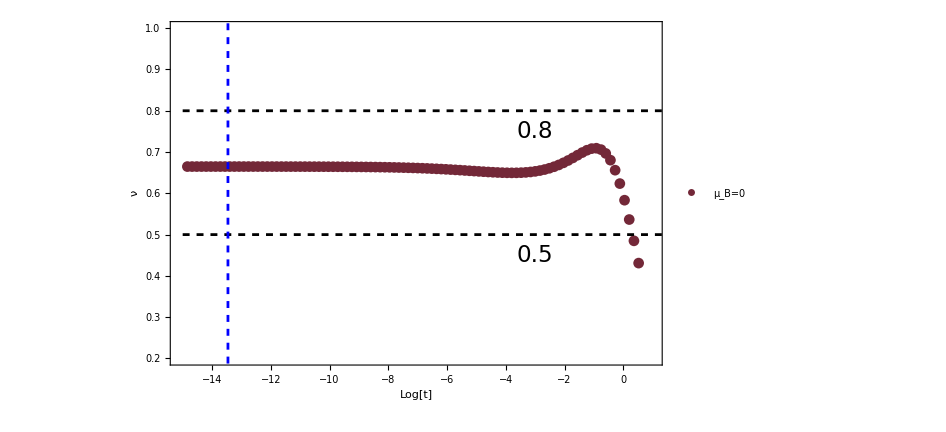

```mathematica
plotT=Show[ListPlot[{b1mub0},
Frame->True,FrameLabel->{Style["Log[t]",25,FontFamily->"Times",Black],Style["ν",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.15}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_B=0","μ_B=700 MeV","μ_B=705 MeV","μ_B=706 MeV","μ_B=706.3 MeV","μ_B=706.4 MeV","TCP ?"},LabelStyle->16],{0.4,0.75}],
PlotRange->{{-15.1,1},{0.2,1}},AxesOrigin->{-15.1,0.3},FrameTicksStyle->Directive[15,Black]],
ListLinePlot[{{-15,0.8},{10,0.8}},PlotStyle->{Black,Dashed}],ListLinePlot[{{-15,0.5},{10,0.5}},PlotStyle->{Black,Dashed}],ListLinePlot[{{-13.4588,0.},{-13.4588,10}},PlotStyle->{Blue,Dashed}],ImageSize->700,Background->None,Epilog->{Text[Style["0.8",23],{-3,0.75}],Text[Style["0.5",23],{-3,0.45}]}]
```

```mathematica
Export["nu_v2.pdf",plotT]
```

nu_v2.pdf